```mathematica
ClearAll["Global`*"]
hbar = 6.582119514*10^(-16)*eV*second;
c = 3*10^8 *meters/second;
n1 = 1;
n2 = 2;

Z = 3;
slope = 0.0246136
const = -0.0711459

νKA = 13.6*eV*(Z - 1)^2*(1/n1^2 - 1/n2^2)/hbar
EKA = νKA*hbar
λKA = (hbar*c)/EKA /. meters-> 10^(9)*nm
BinKA = (EKA/(1000*eV)- const)/slope
```

0.0246136

-0.0711459

(6.19861×10^16)/second

40.8 eV

4.83979 nm

4.54813

```mathematica
n2 = 3;

νKB = 13.6*eV*(Z - 1)^2*(1/n1^2 - 1/n2^2)/hbar
EKB = νKB*hbar
λKB = (hbar*c)/EKB
BinKB = (EKB/(1000*eV)-const)/slope
```

(7.3465×10^16)/second

48.3556 eV

4.08358×10^-9 meters

4.8551

```mathematica
n1 = 2;
n2 = 3;

νLA = 13.6*eV*(Z - 7.4)^2*(1/n1^2 - 1/n2^2)/hbar
ELA = νLA*hbar
λLA = (hbar*c)/ELA
BinLA = (ELA/(1000*eV)- const )/slope
```

(5.20787×10^18)/second

3427.88 eV

5.76052×10^-11 meters

142.158

1.54968×10^16 (-1+Zvar)^2

1.54968×10^16 (-7.4+Zvar)^2

{1.24486×10^8 √((-1+Zvar)^2),Zvar}

{1.24486×10^8 √((-7.4+Zvar)^2),Zvar}

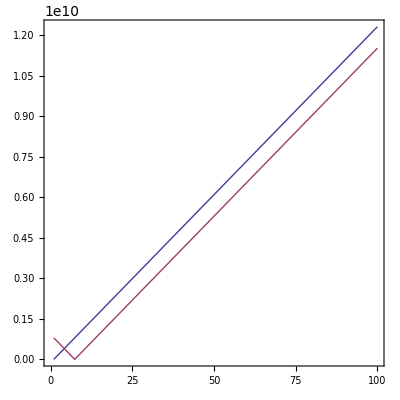

```mathematica
n1 = 1;
n2 = 2;
νKA = 13.6*eV*(Zvar - 1)^2*(1/n1^2 - 1/n2^2)/hbar *second
νLA = 13.6*eV*(Zvar - 7.4)^2*(1/n1^2 - 1/n2^2)/hbar * second
KA = {Sqrt[νKA],Zvar}
LA = {Sqrt[νLA],Zvar}
ParametricPlot[{{KA[[2]],KA[[1]]},{LA[[2]],LA[[1]]}},{Zvar,1,100}, AspectRatio->1, Frame->True, LabelStyle->Directive[Fontsize->20]]
```

```mathematica
Energy = 94.665
(Energy+ 8.25988)/0.0570663
```

94.665

1803.6

```mathematica
Bin = 400
Energy = Bin *0.0570663 - 8.25988
```

400

14.5666

```mathematica
ClearAll["Global`*"]
h = 4.135668*10^(-15)*eV*second;
c = 3*10^8 *meters/second;

(* Scandium anode *)

EKA =(4090.6+ 4086.1)/2*eV
λKA = (h*c)/EKA /. meters-> 10^(9)*nm

EKB =4460.5*eV
λKB = (h*c)/EKB/. meters-> 10^(9)*nm
```

4088.35 eV

0.303472 nm

4460.5 eV

0.278153 nm

```mathematica
d = 629.2 *pm /. pm->10^-3 nm (* KCl *)
n = 1

ArcSin[n*λKA/(2*d)]*(180/Pi)*2
ArcSin[n*λKB/(2*d)]*(180/Pi)*2

n = 2
ArcSin[n*λKA/(2*d)]*(180/Pi)*2
ArcSin[n*λKB/(2*d)]*(180/Pi)*2

n = 3
ArcSin[n*λKA/(2*d)]*(180/Pi)*2
ArcSin[n*λKB/(2*d)]*(180/Pi)*2

n = 4
ArcSin[n*λKA/(2*d)]*(180/Pi)*2
ArcSin[n*λKB/(2*d)]*(180/Pi)*2
```

0.6292 nm

1

27.9097

25.5399

2

57.6733

52.4725

3

92.6837

83.0751

4

149.431

124.294